# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll102`"
<<"HornSchunck`"

methods={"","SemiConstrained","Constrained","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"final"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
dims={412,176};
nx=1;
ny=1;

tim=1;
{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+dims[[2]]*tim},{nx,nx+dims[[1]]*tim}]&/@{ia,ib,id,io}

ims={{iaa,ibb,idd,ioo}}
max=MinMax[Flatten[ImageData[idd]*0.1]][[2]];
Print["max dv=", max]
ImageDimensions[idd]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

max dv=3.86009

{413,177}

```mathematica
(*ListAnimate[{iaa,iaaa}];*)
ListAnimate[{iaa,ibb}];
```

## Big Tests

### Test Run

```mathematica
depth=stereoDepth[ims[[1,1]],ims[[1,2]],ims[[1,3]],0,"HornSchunck"];
```

```mathematica
scale={-10*0.1,0};
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];

RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];

affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
```

```mathematica
pos=Table[{x,depth[[y,x]]},{y,ImageDimensions[ims[[1,1]]][[2]]},{x,ImageDimensions[ims[[1,1]]][[1]]}];
```

```mathematica
posSelect=Select[#,scale[[1]]<#[[2]]<scale[[2]]&]&/@pos;
```

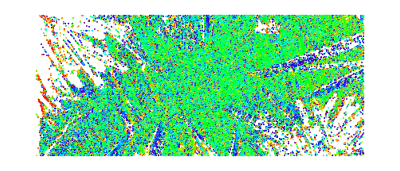

```mathematica
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@posSelect[[y]],{y,1,1+dims[[2]]*tim}]}]
```

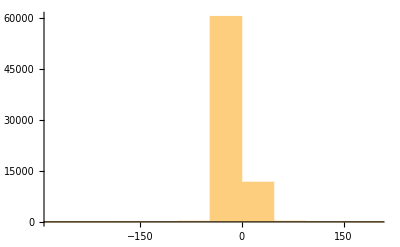

```mathematica
Histogram[Flatten[depth]]
```

```mathematica
imagesTable=Table[

solution=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]]*0.1,scale,{0,1}]]}]];

images=ConformImages[Rasterize[Image[#],ImageResolution->200]&/@Flatten[{Show[ims[[1,1]],g0],solution}],{1000}]


,{which,Length[ims]}];
```

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100];
```

```mathematica
imFinal=Legended[Grid[imagesTable],legendBar]
```

-Graphics- | -Graphics-

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],Rasterize[imFinal,ImageSize->500,ImageResolution->100]]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\figs\sintel-bamboo102-final-HS-im.pdf

### More numbers

```mathematica
depth2=Table[If[scale[[1]]<depth[[y,x]]<scale[[2]],depth[[y,x]],0],{y,1,1+dims[[2]]*tim},{x,1,1+dims[[1]]*tim}];
```

```mathematica
Dimensions[depth2]
Dimensions[depth]
```

{177,413}

{177,413}

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

solution=ImageData[-ims[[which,3]]*0.1];



rmse=Sqrt[Mean[Flatten[(solution-depth2)^2]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,1.14831,Density= ,density}}